```mathematica
(*l–mode Poisson Green's function (regular at 0,decays at Infinity)*)ClearAll[gL,PhiL]

gL[l_Integer?NonNegative,r_,rp_]:=(4 Pi/(2 l+1))*(Min[r,rp]^l/Max[r,rp]^(l+1));

(*Given an l–mode radial source S_l[r],the solution is*)
PhiL[l_Integer?NonNegative,r_,Sl_]:=Integrate[gL[l,r,rp]*Sl[rp]*rp^2,{rp,0,Infinity},Assumptions->{r>0}];

(*Optional:piecewise form (often helps Integrate/NIntegrate)*)
gLpw[l_Integer?NonNegative,r_,rp_]:=(4 Pi/(2 l+1))*Piecewise[{{rp^l/r^(l+1),rp<=r},{r^l/rp^(l+1),rp>=r}}];

PhiLpw[l_Integer?NonNegative,r_,Sl_]:=Integrate[gLpw[l,r,rp]*Sl[rp]*rp^2,{rp,0,Infinity},Assumptions->{r>0}];

(*Example usage:Define a source mode S_l(r) and compute Φ_l(r)*)
SlExample[r_]:=Exp[-r]  (*replace with your S_l[r]*)

phi2[r_]:=PhiLpw[2,r,SlExample];  (*l=2 mode*)
```

```mathematica
phi2[4]
```

(-103 π+3 ⅇ^4 π-128 ⅇ^4 π ExpIntegralEi[-4])/(10 ⅇ^4)

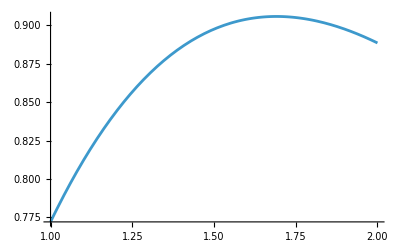

```mathematica
ClearAll[SlExample,PhiLFast,phi2Fast];

SlExample[r_?NumericQ]:=Exp[-r];

PhiLFast[l_Integer?NonNegative,Sl_,r_?NumericQ]:=Module[{pref=4 Pi/(2 l+1),i1,i2},i1=NIntegrate[rp^(l+2) Sl[rp],{rp,0,r},Method->{"LocalAdaptive","SymbolicProcessing"->0}];
i2=NIntegrate[rp^(1-l) Sl[rp],{rp,r,Infinity},Method->{"LocalAdaptive","SymbolicProcessing"->0}];
pref*(i1/r^(l+1)+r^l*i2)];

phi2Fast[r_?NumericQ]:=PhiLFast[2,SlExample,r];

Plot[phi2Fast[r],{r,1,2}]
```

## Calculate Source

```mathematica
ClearAll[PhiLpwSolve];

(*Solves ∇^2 Φ_l=S_l when gLpw is the 1/|x-x'|kernel expansion*)
PhiLpwSolve[l_Integer?NonNegative,r_,Sl_]:=Assuming[r>0,FullSimplify[Integrate[(-1/(4 Pi))*gLpw[l,r,rp]*Sl[rp]*rp^2,{rp,0,Infinity}],r>0]];
```

```mathematica
z0=5
```

5

```mathematica
ClearAll[SdeltaAnalyticmodes,SdeltaAnalyticmodesF];

SdeltaAnalyticmodes[l_Integer?NonNegative,r_]:=FullSimplify[Integrate[Integrate[(-4 Pi) DiracDelta[r-z0]/r^2*DiracDelta[μ-1]*DiracDelta[ϕ-Pi]*SphericalHarmonicY[l,0,ArcCos[μ],ϕ],{μ,-1,1}],{ϕ,0,2 Pi}],Assumptions->{r∈Reals,z0∈Reals,r>0}]/. HeavisideTheta[0]->1;

(*Make it a function of the dummy integration variable*)
SdeltaAnalyticmodesF[l_Integer?NonNegative]:=Function[{rp},Evaluate[SdeltaAnalyticmodes[l,rp]]];
```

```mathematica
(*Solves ∇^2 Φ_l=S_l when gLpw is the 1/|x-x'|kernel expansion*)PhiLpwSolve[l_Integer?NonNegative,r_,Sl_]:=Assuming[r>0,FullSimplify[Integrate[(-1/(4 Pi))*gLpw[l,r,rp]*Sl[rp]*rp^2,{rp,0,Infinity}],r>0]];
```

```mathematica
ld=0;
PhiLpw0Delta=PhiLpwSolve[ld,r,SdeltaAnalyticmodesF[ld]]//FullSimplify
```

2 √π (Piecewise[{{1/5, r<5}, {1/r, True}}])

```mathematica
ldmax=50
```

50

```mathematica
Do[
PhiLpwDelta[ld]=PhiLpwSolve[ld,r,SdeltaAnalyticmodesF[ld]]//FullSimplify;
plt[ld]=Plot[PhiLpwDelta[ld],{r,0,10}];
,{ld,0,ldmax}]
```

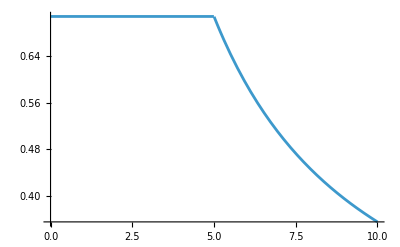
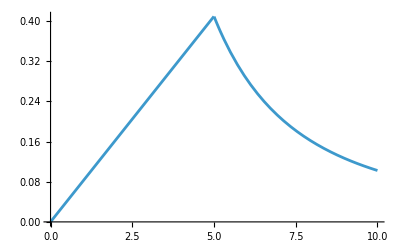
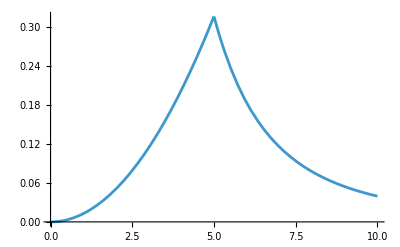
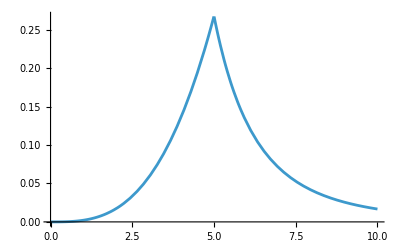
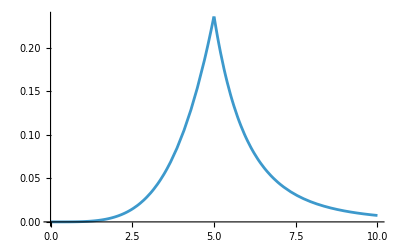
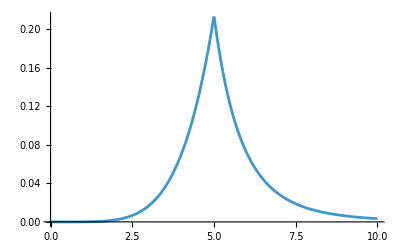
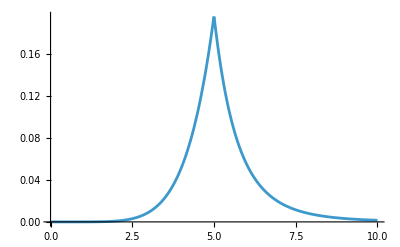
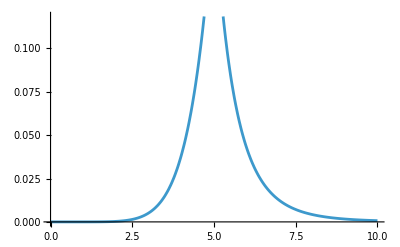

```mathematica
Table[plt[ld],{ld,0,ldmax}]
```

## Solve the Greens function on a contour

### Source, Extended Dirac Delta function

```mathematica
HLog[r_,r0_]:=1+ I/Pi Log[r-r0]
```

```mathematica
ExtendedDiracDelta=D[HLog[rp$,5],rp$]
```

ⅈ/(π (-5+rp$))

```mathematica
Do[
ExtendedDiracSource[n]=SdeltaAnalyticmodesF[n]/.DiracDelta[__]->ExtendedDiracDelta;
, {n,0,ldmax}]
```

```mathematica
SdeltaAnalyticmodesF[0]
```

Function[{rp$},-2/25 √π DiracDelta[-5+rp$]]

```mathematica
ExtendedDiracSource[0]
```

Function[{rp$},-(2 √π ⅈ)/(25 (π (-5+rp$)))]

## Contour

```mathematica
J=1;
width=1;
γ[a_]:=a+I J Exp[-width(a-z0)^2];
γp[a_]:=D[γ[a],a];

γpp[a_]:=D[γ[a],{a,2}];

(*l–mode kernel for 1/|x-x'|(your earlier gLpw)*)
gLpw[l_Integer?NonNegative,r_,rp_]:=(4 Pi/(2 l+1))*Piecewise[{{rp^l/r^(l+1),rp<=r},{r^l/rp^(l+1),rp>=r}}];

(*Your source mode as a function of rp (example:l=0 delta-mode you built)*)
(*Assumes you already have SdeltaAnalyticmodesF[l] defined*)
(*SdeltaAnalyticmodesF[l_Integer?NonNegative]:=Function[{rp},...];*)

(*Contour-convolution for ∇^2 Φ_l=S_l with 1/|x-x'|kernel*)
PhiLContour[l_Integer?NonNegative,r_,Sl_,{a_,a0_,a1_}]:=NIntegrate[(-1/(4 Pi))*gLpw[l,r,γ[a]]*ExtendedDiracSource[0,γ[a]]*(γ[a]^2)*γp[a],{a,a0,a1},Method->{"LocalAdaptive","SymbolicProcessing"->0},WorkingPrecision->50,AccuracyGoal->20,PrecisionGoal->20];
```

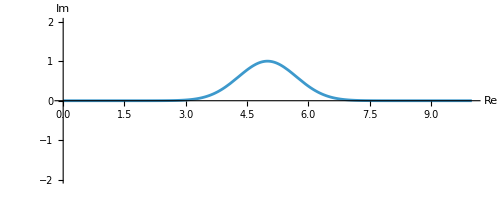

```mathematica
ParametricPlot[{Re[γ[a]],Im[γ[a]]},{a,0,10},AxesLabel->{"Re","Im"},PlotRange->{All,{-2,2}}]
```

## Integrate along contour

```mathematica
ClearAll[BuildPhiLContourFast];

BuildPhiLContourFast[l_Integer?NonNegative,Sl_,{a0_?NumericQ,a1_?NumericQ},n_Integer:2000,wp_Integer:40]:=Module[{pref=-1/(2 l+1),agrid,da,Fvals,Gvals,Avals,Bvals,Aifun,Bifun,B1},(*contour*)γ[a_]:=a+I J Exp[-width (a-z0)^2];
γp[a_]:=1+I J Exp[-width (a-z0)^2]*(-2 width (a-z0));
agrid=SetPrecision[Subdivide[a0,a1,n],wp];
da=Differences[agrid];
(*sample integrands*)Fvals=γ[#]^(l+2)*Sl[γ[#]]*γp[#]&/@agrid;
Gvals=γ[#]^(1-l)*Sl[γ[#]]*γp[#]&/@agrid;
(*cumulative trapezoid integrals*)Avals=Prepend[Accumulate[da*(Most[Fvals]+Rest[Fvals])/2],0];
Bvals=Prepend[Accumulate[da*(Most[Gvals]+Rest[Gvals])/2],0];
Aifun=Interpolation[Transpose[{agrid,Avals}],InterpolationOrder->1];
Bifun=Interpolation[Transpose[{agrid,Bvals}],InterpolationOrder->1];
B1=Bifun[a1];
Function[{r},Module[{rr=N[r]},If[rr<a0||rr>a1,Indeterminate,pref*(Aifun[rr]/rr^(l+1)+rr^l*(B1-Bifun[rr]))]]]];
```

```mathematica
Monitor[Do[phiContour[ld]=BuildPhiLContourFast[ld,ExtendedDiracSource[ld],{0.05,10},3000,40];
pltCont[ld]=Plot[{Re@phiContour[ld][r],Im@phiContour[ld][r],PhiLpwDelta[ld]},{r,1,9},PlotRange->All];
,{ld,0,ldmax}],ld]
```

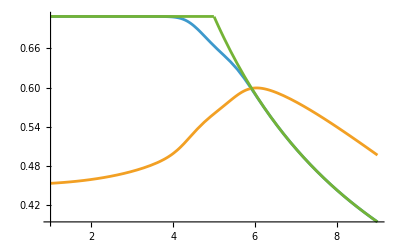
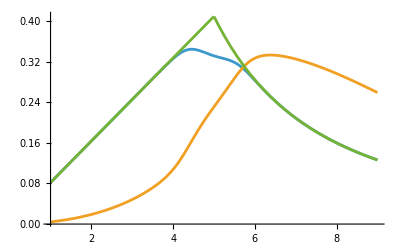
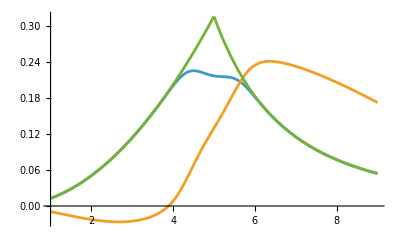
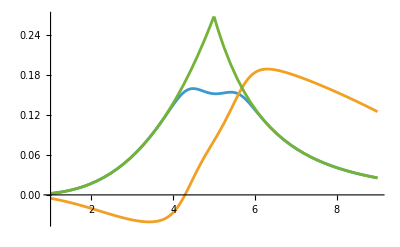
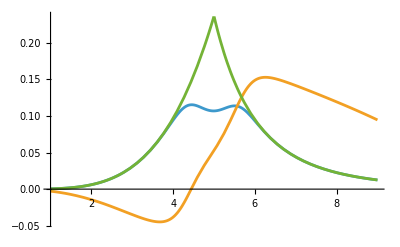
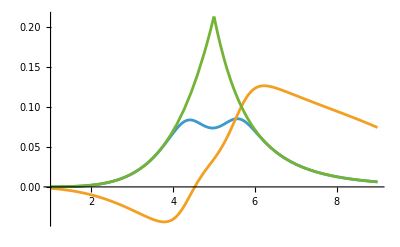
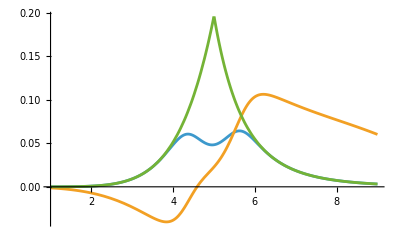
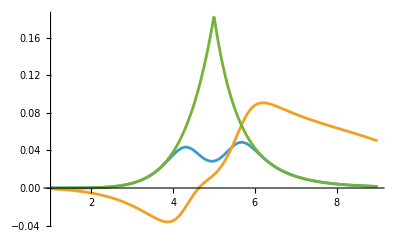

```mathematica
Table[{pltCont[n]},{n,0,ldmax}]
```

```mathematica
Do[ErrorPlot[ld]=LogLogPlot[Abs[(Re[phiContour[ld][r]]-(Re[PhiLpwDelta[ld]]))/(Re[phiContour[ld][r]])],{r,1,10},PlotLegends->{"Contour Error"Row[{"Error l=",ld}]},AxesLabel->{"x","error"},PlotRange->All,ImageSize->500],
{ld,0,ldmax}]
```

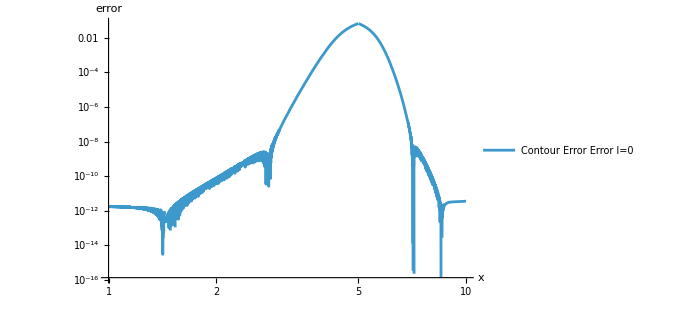
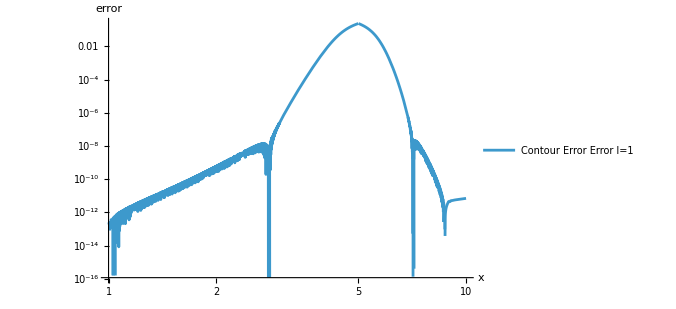
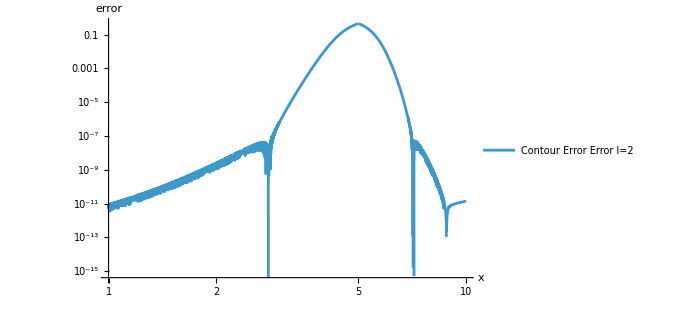
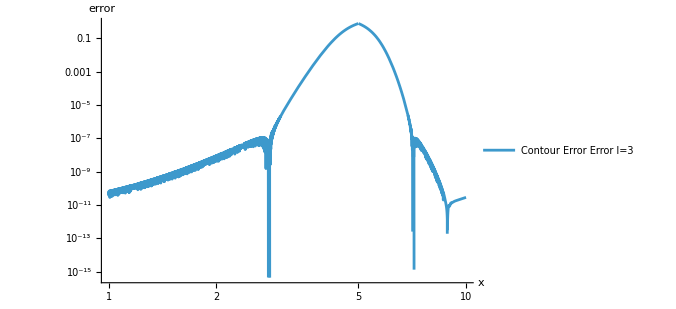
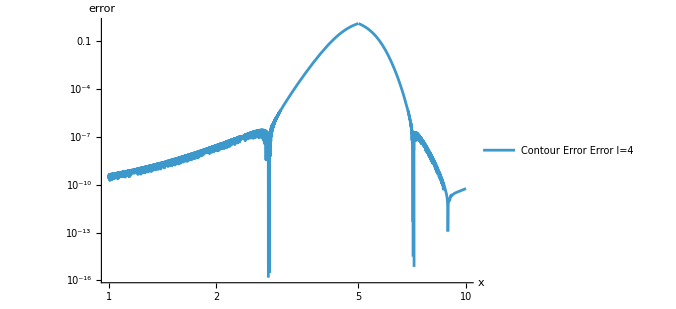
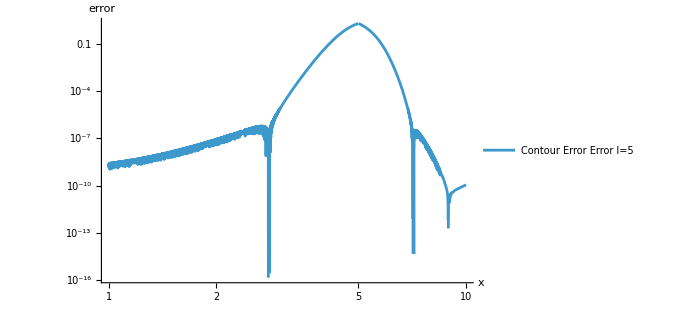
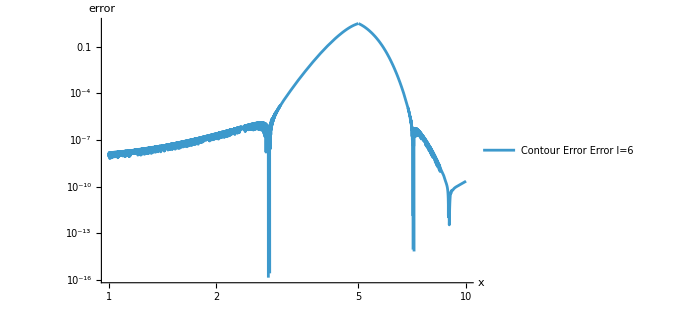
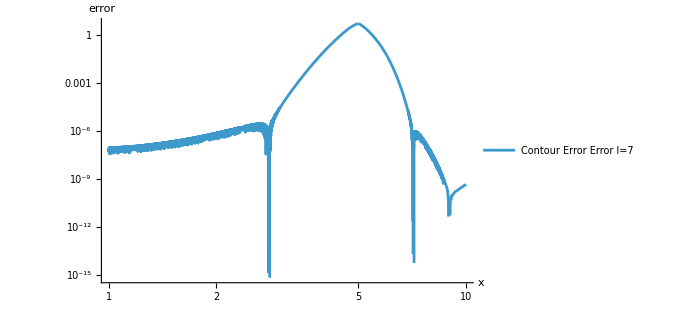
{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
Table[{ErrorPlot[n]},{n,0,ldmax}]
```

## Check it works at second-order

## second-order source modes

```mathematica
Source=Function[{r,θ,z0}, 1/(r^2+z0^2-2z0 r Cos[θ])]
```

Function[{r,θ,z0},1/(r^2+z0^2-2 z0 r Cos[θ])]

```mathematica
S3D=Function[{x,y,z,z0},1/((x^2+y^2+(z-z0)^2))]
```

Function[{x,y,z,z0},1/(x^2+y^2+(z-z0)^2)]

```mathematica
Source[r,θ,z0d]-S3D[r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ],z0d]//FullSimplify
```

0

```mathematica
rho=Function[{a,b,θ},1/(a(1-b Cos[θ]))]
```

Function[{a,b,θ},1/(a (1-b Cos[θ]))]

```mathematica
afunc=r^2+z0^2
```

25+r^2

```mathematica
bfuncNoAbs=2z0 r/afunc
```

(10 r)/(25+r^2)

```mathematica
SAnalyticmodes[l_]:=2Pi Integrate[rho[a,b,θ]SphericalHarmonicY[l,0,θ,ϕ]Sin[θ],{θ,0,Pi},Assumptions->{a∈Reals,b∈Reals,θ∈Reals,r∈Reals,z0∈Reals}]//Normal//Simplify
```

```mathematica
S[0]=SAnalyticmodes[0]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

(√π Log[(5+r)^2/(-5+r)^2])/(10 r)

```mathematica
S[1]=SAnalyticmodes[1]/.{a->afunc,b->bfuncNoAbs}
```

-(√(3 π) (25+r^2) ((10 r)/(25+r^2)-ArcTanh[(10 r)/(25+r^2)]))/(50 r^2)

```mathematica
(*S[2]=SAnalyticmodes[2]/.{a->afunc,b->bfuncNoAbs}*)
```

```mathematica
(*S[3]=SAnalyticmodes[3]/.{a->afunc,b->bfuncNoAbs}*)
```

```mathematica
(*S[4]=SAnalyticmodes[4]/.{a->afunc,b->bfuncNoAbs}*)
```

```mathematica
(*S[5]=SAnalyticmodes[5]/.{a->afunc,b->bfuncNoAbs}*)
```

## Second-order source mode sum

### l=0

```mathematica
SecondOrderTestSource=PhiLpwDelta[ld]^2
```

4 π (Piecewise[{{1/5, r<5}, {1/r, True}}])^2

```mathematica
CIntrule={CInt[xAct`xTensor`LI[l_],xAct`xTensor`LI[m_],xAct`xTensor`LI[s_],-xAct`xTensor`LI[l1_],-xAct`xTensor`LI[m1_],-xAct`xTensor`LI[s1_],-xAct`xTensor`LI[l2_],-xAct`xTensor`LI[m2_],-xAct`xTensor`LI[s2_]]:>(-1)^(m+s)Sqrt[(2l+1)(2l1+1)(2l2+1)/(4 Pi)]ThreeJSymbol[{l,s},{l1,-s1},{l2,-s2}]ThreeJSymbol[{l,-m},{l1,m1},{l2,m2}]}
```

{CInt[xAct`xTensor`LI[l_],xAct`xTensor`LI[m_],xAct`xTensor`LI[s_],-xAct`xTensor`LI[l1_],-xAct`xTensor`LI[m1_],-xAct`xTensor`LI[s1_],-xAct`xTensor`LI[l2_],-xAct`xTensor`LI[m2_],-xAct`xTensor`LI[s2_]]:>(-1)^(m+s) √(((2 l+1) (2 l1+1) (2 l2+1))/(4 π)) ThreeJSymbol[{l,s},{l1,-s1},{l2,-s2}] ThreeJSymbol[{l,-m},{l1,m1},{l2,m2}]}

```mathematica
Source={{C, {{l, m, 0, , , , , , }, {, , , l2, m2, 0, l1, m1, 0}}}} Phi[l1]Phi[l2]/.CIntrule/.{m->0,m1->0,m2->0}
```

1/(2 √π)√((1+2 l) (1+2 l1) (1+2 l2)) Phi[l1] Phi[l2] (Piecewise[{{1/((-1/2-l/2+l1/2-l2/2)!)(-1)^(l-l2) 2^(-1/2+l-l1+l2) π^(1/4) √((2^(-l+l1-l2) (-1/2+l/2+l1/2-l2/2)! (-1/2-l/2+l1/2+l2/2)! (l/2+l1/2+l2/2)!)/((l/2+l1/2-l2/2)! (-l/2+l1/2+l2/2)! (1/2+l/2+l1/2+l2/2)! (l-l1+l2)!)), l∈ℤ&&l1∈ℤ&&l2∈ℤ&&l≥0&&l1≥0&&l2≥0&&l≤l1+l2&&l1≤l+l2&&l2≤l+l1}, {0, True}}])^2

```mathematica
Sourcel[ld_]:=Sum[Source/.l->ld/.l1->ld1/.l2->ld2,{ld1,0,ldmax},{ld2,0,ldmax}]
```

```mathematica
Sourcel[0]
```

Phi[0]^2/(2 √π)+Phi[1]^2/(2 √π)+Phi[2]^2/(2 √π)+Phi[3]^2/(2 √π)+Phi[4]^2/(2 √π)+Phi[5]^2/(2 √π)+Phi[6]^2/(2 √π)+Phi[7]^2/(2 √π)+Phi[8]^2/(2 √π)+Phi[9]^2/(2 √π)+Phi[10]^2/(2 √π)+Phi[11]^2/(2 √π)+Phi[12]^2/(2 √π)+Phi[13]^2/(2 √π)+Phi[14]^2/(2 √π)+Phi[15]^2/(2 √π)+Phi[16]^2/(2 √π)+Phi[17]^2/(2 √π)+Phi[18]^2/(2 √π)+Phi[19]^2/(2 √π)+Phi[20]^2/(2 √π)+Phi[21]^2/(2 √π)+Phi[22]^2/(2 √π)+Phi[23]^2/(2 √π)+Phi[24]^2/(2 √π)+Phi[25]^2/(2 √π)+Phi[26]^2/(2 √π)+Phi[27]^2/(2 √π)+Phi[28]^2/(2 √π)+Phi[29]^2/(2 √π)+Phi[30]^2/(2 √π)+Phi[31]^2/(2 √π)+Phi[32]^2/(2 √π)+Phi[33]^2/(2 √π)+Phi[34]^2/(2 √π)+Phi[35]^2/(2 √π)+Phi[36]^2/(2 √π)+Phi[37]^2/(2 √π)+Phi[38]^2/(2 √π)+Phi[39]^2/(2 √π)+Phi[40]^2/(2 √π)+Phi[41]^2/(2 √π)+Phi[42]^2/(2 √π)+Phi[43]^2/(2 √π)+Phi[44]^2/(2 √π)+Phi[45]^2/(2 √π)+Phi[46]^2/(2 √π)+Phi[47]^2/(2 √π)+Phi[48]^2/(2 √π)+Phi[49]^2/(2 √π)+Phi[50]^2/(2 √π)

```mathematica
Sourcelsum[l_,l1_][r_?NumericQ]:=Module[{rr=N[r,10],expr},expr=(Sourcel[l]/. Table[Phi[ldmax-n]->0,{n,0,ldmax-l1}])/. {Phi[n_]:>Re[phiContour[n][rr]]}/. z0->5;
N[expr,10]]
```

```mathematica
Sourcelsum[0,1][5]
NumberQ[%]
```

0.124317

True

```mathematica
ClearAll[SourcelsumExpr,SourcelsumFast];

SourcelsumExpr[l_,l1_]:=Sourcel[l]/. Table[Phi[ldmax-n]->0,{n,0,ldmax-l1}]/. z0->5;

SourcelsumFast[l_,l1_]:=Module[{expr},expr=SourcelsumExpr[l,l1];
Function[{r},N[expr/. Phi[n_]:>Re[phiContour[n][r]],30]]]
```

```mathematica
src01=SourcelsumFast[0,1]
```

Function[{r$},N[expr$293203/.Phi[n$_]:>Re[phiContour[n$][r$]],30]]

```mathematica
src05=SourcelsumFast[0,5]
```

Function[{r$},N[expr$293204/.Phi[n$_]:>Re[phiContour[n$][r$]],30]]

```mathematica
src020=SourcelsumFast[0,20]
```

Function[{r$},N[expr$293206/.Phi[n$_]:>Re[phiContour[n$][r$]],30]]

```mathematica
LogPlot[{S[0],src[2][r],src01[r],src05[r],src020[r]},{r,1,10},PlotRange->All]
```

-Graphics-

```mathematica
Convergencetest=Table[Sourcelsum[0,q][5]-Sourcelsum[0,q-1][5],{q,1,ldmax}]
```

{0.124317,0.0310004,0.0133425,0.00649193,0.00321854,0.00153344,0.000660697,0.000231987,0.0000499005,5.76752×10^-7,0.0000159836,0.0000554864,0.0000958232,0.000125466,0.00014517,0.0000661187,0.0000521449,0.0000375339,0.0000240688,0.0000130669,5.30898×10^-6,1.04173×10^-6,3.76082×10^-8,1.69917×10^-6,5.18948×10^-6,9.57135×10^-6,0.0000139392,0.0000175294,0.0000197997,0.0000204716,0.0000195342,0.0000172147,0.0000139206,0.0000101646,6.48343×10^-6,3.3603×10^-6,1.16189×10^-6,9.61473×10^-8,1.95063×10^-7,1.3229×10^-6,3.20696×10^-6,5.48523×10^-6,7.76351×10^-6,9.67352×10^-6,0.000010924,0.0000113385,0.0000108744,9.62237×10^-6,7.78721×10^-6,5.65245×10^-6}

```mathematica
ListPlot[Convergencetest]
```

-Graphics-

```mathematica
Show[ListLogLogPlot[Convergencetest],LogLogPlot[0.001/l,{l,1,50}]]
```

-Graphics-

```mathematica
expr=Sourcelsum[0,1];
expr/. _Symbol?(Function[s,SymbolName[s]=="r"])->5
```

Sourcelsum[0,1]

```mathematica
Cases[expr,s_Symbol/;SymbolName[s]=="r":>{s,Context[s]},Infinity]
```

{}

```mathematica
expr/. r->5
```

Sourcelsum[0,1]

```mathematica
expr=Sourcelsum[0,1];

expr/. r->5

N[expr/. r->5,30]

FullForm[expr/. r->5]
```

Sourcelsum[0,1]

Sourcelsum[0,1.]

Sourcelsum[0,1]

```mathematica
LogPlot[{S[0],Sourcel[0]/.Table[Phi[ldmax-n]->0,{n,0,9}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[0]/.Table[Phi[ldmax-n]->0,{n,0,7}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[0]/.Table[Phi[ldmax-n]->0,{n,0,5}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[0]/.Table[Phi[ldmax-n]->0,{n,0,3}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,
Sourcel[0]/.Table[Phi[ldmax-n]->0,{n,0,1}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[0]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5},{r,1,10},PlotRange->All]
```

$Aborted

```mathematica
ldmax=20
```

20

```mathematica
Sourcel[ld_]:=Sum[Source/.l->ld/.l1->ld1/.l2->ld2,{ld1,0,ldmax},{ld2,0,ldmax}]
```

```mathematica
LogPlot[{S[0],Sourcel[0]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5},{r,1,10},PlotRange->All]
```

-Graphics-

```mathematica
Source2[0]=Sourcel[0]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5;
```

### l=1

```mathematica
ldmax=10
```

10

```mathematica
Sourcel[ld_]:=Sum[Source/.l->ld/.l1->ld1/.l2->ld2,{ld1,0,ldmax},{ld2,0,ldmax}]
```

```mathematica
Sourcel[1]
```

(Phi[0] Phi[1])/(√π)+(2 Phi[1] Phi[2])/(√(5 π))+3 √(3/(35 π)) Phi[2] Phi[3]+(4 Phi[3] Phi[4])/(√(21 π))+(5 Phi[4] Phi[5])/(√(33 π))+6 √(3/(143 π)) Phi[5] Phi[6]+(7 Phi[6] Phi[7])/(√(65 π))+(8 Phi[7] Phi[8])/(√(85 π))+9 √(3/(323 π)) Phi[8] Phi[9]+(10 Phi[9] Phi[10])/(√(133 π))

```mathematica
LogPlot[{S[1],Sourcel[1]/.Table[Phi[ldmax-n]->0,{n,0,9}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[1]/.Table[Phi[ldmax-n]->0,{n,0,7}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[1]/.Table[Phi[ldmax-n]->0,{n,0,5}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[1]/.Table[Phi[ldmax-n]->0,{n,0,3}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,
Sourcel[1]/.Table[Phi[ldmax-n]->0,{n,0,1}]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5,Sourcel[1]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5},{r,1,10},PlotRange->All]
```

-Graphics-

```mathematica
ldmax=20
```

20

```mathematica
Sourcel[ld_]:=Sum[Source/.l->ld/.l1->ld1/.l2->ld2,{ld1,0,ldmax},{ld2,0,ldmax}]
```

```mathematica
LogPlot[{S[1],Sourcel[1]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5},{r,1,10},PlotRange->All]
```

-Graphics-

```mathematica
Source2[1]=Sourcel[1]/.{Phi[n_]:>Re[phiContour[n][r]]}/.z0->5;
```

## Solve second-order ODE

```mathematica
z0d=z0
```

5

```mathematica
AnalyticSol=(√π (-4 r z0-(r-z0)^2 Log[(r-z0)^2]+(r+z0)^2 Log[(r+z0)^2]))/(4 r z0)
```

(√π (-20 r-(-5+r)^2 Log[(-5+r)^2]+(5+r)^2 Log[(5+r)^2]))/(20 r)

```mathematica
BoundaryConditions={AnalyticSol/.r->1,D[AnalyticSol,r]/.r->1}
```

{1/20 √π (-20-16 Log[16]+36 Log[36]),1/20 √π (8 Log[16]+12 Log[36])-1/20 √π (-20-16 Log[16]+36 Log[36])}

```mathematica
γpp[a_]:=D[γ[a],{a,2}];
```

```mathematica
ContourODEHomo=Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+2γp[a]/γ[a]) Y'[a]-l(l+1)γp[a]^2/γ[a]^2Y[a]==γp[a]^2 * (Source2[l]/.r->γ[a])]
```

Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+(2 γp[a])/γ[a]) Y'[a]-(l (l+1) γp[a]^2 Y[a])/γ[a]^2==γp[a]^2 (Source2[l]/.r→γ[a])]

```mathematica
ContourODEHomo0=ContourODEHomo[a,0];
```

```mathematica
(*Solve along the contour:Y(a)=ψ(γ(a)) numerically *)
solNumericCont=NDSolveValue[{ContourODEHomo[a,0],Y[1]==BoundaryConditions[[1]],Y'[1]==BoundaryConditions[[2]]},Y,{a,1,100},WorkingPrecision->50]
```

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at a == 1..

NDSolveValue[{Y'[a] ((2 gammaSquarePrime[a])/gammaSquare[a]-gammaSquare''[a]/gammaSquarePrime[a])+Y''[a]==gammaSquarePrime[a]^2 (1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$1037714 (Aifun$1037714[rr$6966023]/rr$6966023^(3+1)+rr$6966023^3 (B1$1037714-Bifun$1037714[rr$6966023]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$1334004 (Aifun$1334004[rr$6966024]/rr$6966024^(4+1)+rr$6966024^4 (B1$1334004-Bifun$1334004[rr$6966024]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$149419 (Aifun$149419[rr$6966020]/rr$6966020^(0+1)+rr$6966020^0 (B1$149419-Bifun$149419[rr$6966020]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$1630296 (Aifun$1630296[rr$6966025]/rr$6966025^(5+1)+rr$6966025^5 (B1$1630296-Bifun$1630296[rr$6966025]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$1926596 (Aifun$1926596[rr$6966026]/rr$6966026^(6+1)+rr$6966026^6 (B1$1926596-Bifun$1926596[rr$6966026]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$2222980 (Aifun$2222980[rr$6966027]/rr$6966027^(7+1)+rr$6966027^7 (B1$2222980-Bifun$2222980[rr$6966027]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$2519410 (Aifun$2519410[rr$6966028]/rr$6966028^(8+1)+rr$6966028^8 (B1$2519410-Bifun$2519410[rr$6966028]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$2816200 (Aifun$2816200[rr$6966029]/rr$6966029^(9+1)+rr$6966029^9 (B1$2816200-Bifun$2816200[rr$6966029]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$3113095 (Aifun$3113095[rr$6966030]/rr$6966030^(10+1)+rr$6966030^10 (B1$3113095-Bifun$3113095[rr$6966030]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$3410028 (Aifun$3410028[rr$6966031]/rr$6966031^(11+1)+rr$6966031^11 (B1$3410028-Bifun$3410028[rr$6966031]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$3707078 (Aifun$3707078[rr$6966032]/rr$6966032^(12+1)+rr$6966032^12 (B1$3707078-Bifun$3707078[rr$6966032]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$4004108 (Aifun$4004108[rr$6966033]/rr$6966033^(13+1)+rr$6966033^13 (B1$4004108-Bifun$4004108[rr$6966033]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$4301133 (Aifun$4301133[rr$6966034]/rr$6966034^(14+1)+rr$6966034^14 (B1$4301133-Bifun$4301133[rr$6966034]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$445340 (Aifun$445340[rr$6966021]/rr$6966021^(1+1)+rr$6966021^1 (B1$445340-Bifun$445340[rr$6966021]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$4598075 (Aifun$4598075[rr$6966035]/rr$6966035^(15+1)+rr$6966035^15 (B1$4598075-Bifun$4598075[rr$6966035]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$4897400 (Aifun$4897400[rr$6966036]/rr$6966036^(16+1)+rr$6966036^16 (B1$4897400-Bifun$4897400[rr$6966036]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$5198518 (Aifun$5198518[rr$6966037]/rr$6966037^(17+1)+rr$6966037^17 (B1$5198518-Bifun$5198518[rr$6966037]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$5499836 (Aifun$5499836[rr$6966038]/rr$6966038^(18+1)+rr$6966038^18 (B1$5499836-Bifun$5499836[rr$6966038]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$5797137 (Aifun$5797137[rr$6966039]/rr$6966039^(19+1)+rr$6966039^19 (B1$5797137-Bifun$5797137[rr$6966039]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$6094188 (Aifun$6094188[rr$6966040]/rr$6966040^(20+1)+rr$6966040^20 (B1$6094188-Bifun$6094188[rr$6966040]))]]^2+1/(2 √π)Re[If[gammaSquare[a]<0.05||gammaSquare[a]>10,Indeterminate,pref$741418 (Aifun$741418[rr$6966022]/rr$6966022^(2+1)+rr$6966022^2 (B1$741418-Bifun$741418[rr$6966022]))]]^2),Y[1]==1/20 √π (-20-16 Log[16]+36 Log[36]),Y'[1]==1/20 √π (8 Log[16]+12 Log[36])-1/20 √π (-20-16 Log[16]+36 Log[36])},Y,{a,1,100},WorkingPrecision→50]

```mathematica
ContourODEHomo=Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+2γp[a]/γ[a]) Y'[a]-l(l+1)γp[a]^2/γ[a]^2Y[a]==γp[a]^2 * 0(Source2[l]/.r->γ[a])]
```

Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+(2 γp[a])/γ[a]) Y'[a]-(l (l+1) γp[a]^2 Y[a])/γ[a]^2==γp[a]^2 0 (Source2[l]/.r→γ[a])]

```mathematica
ContourODEHomo0=ContourODEHomo[a,0]
```

Y'[a] ((2 gammaSquarePrime[a])/gammaSquare[a]-gammaSquare''[a]/gammaSquarePrime[a])+Y''[a]==0

```mathematica
(*Solve along the contour:Y(a)=ψ(γ(a)) numerically *)
solNumericCont=NDSolveValue[{ContourODEHomo[a,0],Y[1]==BoundaryConditions[[1]],Y'[1]==BoundaryConditions[[2]]},Y,{a,1,100},WorkingPrecision->50]
```

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point a == 3.5283023980135025949329052049711750905470143745881.

InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000000, 3.5283023980135025949329052049711750905470143745881}}, <>]

```mathematica
Plot[{Re[solNumericCont[a]],Im[solNumericCont[a]],Re[AnalyticSol/.r->a],Im[AnalyticSol/.r->a]},{a,1,10},PlotLegends->{"Re Y (Cont numeric)","Im Y ( Cont numeric)","Re Y (analytic)","Im Y ( analytic)"},AxesLabel->{"a","Y(a)"},PlotRange->All,ImageSize->520,PlotStyle->{{Thick},{Thick},{Dashed,Blue},{Dashed,Red}   }]
```

-Graphics-